```mathematica
data=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/EECS545-Project/results/GreatLakes-with-gpu/15n-0n-on-20n_0420-0820.csv","Numeric"->True];
data=Delete[data, 1];
{baseline, gnn}=GatherBy[data,First];
baseline=Drop[#,{2,3}]&/@(Drop[#,{1,6}]&/@baseline);
gnn=Drop[#,{2,3}]&/@(Drop[#,{1,6}]&/@gnn);
```

```mathematica
(*{stime|walltime|proctime}*)
baselineWall=Part[#,2]&/@baseline;
gnnWall=Part[#,2]&/@gnn;
transferLsize=Min[Length[baselineWall],Length[gnnWall]]
baselineWallnormal=baselineWall[[1;;100]];
baselineWalltransferS=baselineWall[[101;;200]];
baselineWalltransferM=baselineWall[[201;;300]];
baselineWalltransferL=baselineWall[[301;;transferLsize]];
gnnWallnormal=gnnWall[[1;;100]];
gnnWalltransferS=gnnWall[[101;;200]];
gnnWalltransferM=gnnWall[[201;;300]];
gnnWalltransferL=gnnWall[[301;;transferLsize]];
```

302

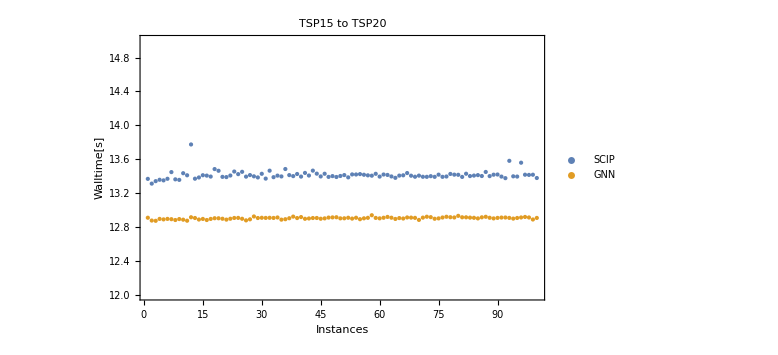

```mathematica
Show[
ListPlot[{baselineWallnormal,gnnWallnormal},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.9}]
],
PlotRange->{Automatic,{12,15}},
PlotLabel->Style["TSP15 to TSP20"],
AxesOrigin->{0,0},
ImageSize->Large
]
```

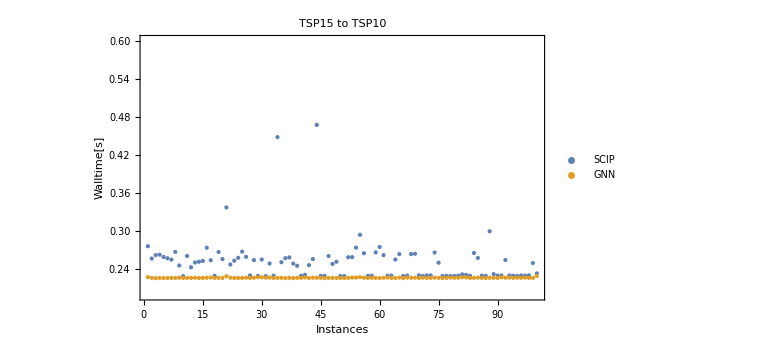

```mathematica
Show[
ListPlot[{baselineWalltransferS,gnnWalltransferS},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.9}]
],
PlotRange->{Automatic,{0.2,0.6}},
PlotLabel->Style["TSP15 to TSP10"],
AxesOrigin->{0,0},
ImageSize->Large
]
```

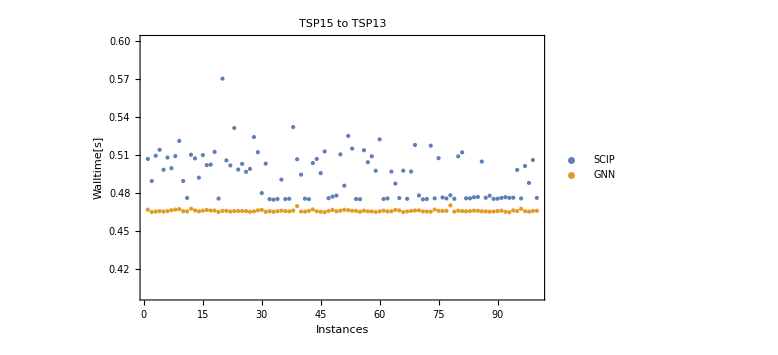

```mathematica
Show[
ListPlot[{baselineWalltransferM,gnnWalltransferM},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.9}]
],
PlotRange->{Automatic,{0.4,0.6}},
PlotLabel->Style["TSP15 to TSP13"],
AxesOrigin->{0,0},
ImageSize->Large
]
```

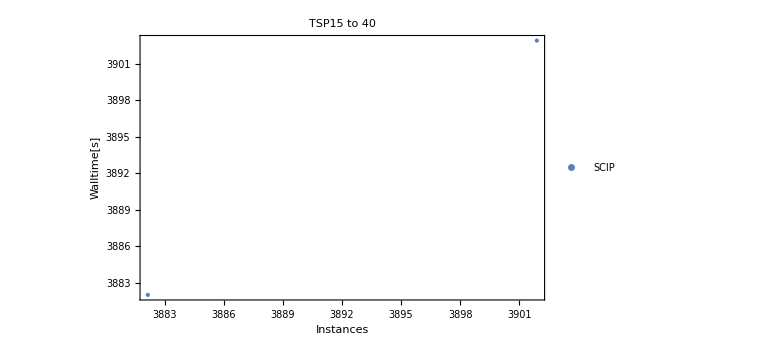

```mathematica
Show[
ListPlot[{baselineWalltransferL,gnnWalltransferL},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.9}]
],
PlotRange->{Automatic,Automatic},
PlotLabel->Style["TSP15 to 40"],
AxesOrigin->{0,0},
ImageSize->Large
]
```